```mathematica
pair[T_] := Exp[ 23.32 - (2831/T)]
```

```mathematica
pair[293]
```

854169.

```mathematica
Ts = {100, 150, 200, 250, 300}
```

{100,150,200,250,300}

```mathematica
Map[ pair, Ts]
```

{0.00680566,85.342,9556.72,162105.,1.07018×10^6}

```mathematica
pwater[T_] := Exp[ 77.34 - (7235/T) - 8.2 Log[T] + 0.005711 T]
```

```mathematica
Map[ pwater, Ts]
```

{1.03551×10^-14,0.0000147555,0.320138,94.8001,3517.89}

```mathematica
pwater[ 273.15 ]
```

608.203

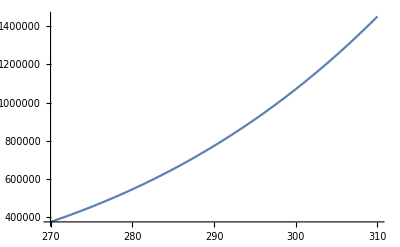

```mathematica
Plot[ pair[t], {t,270, 310}]
```

```mathematica
pair[273+20]
```

854169.

```mathematica
pwater2[T_] := 6.1078 10^(7.5 T /( T + 237.3))
```

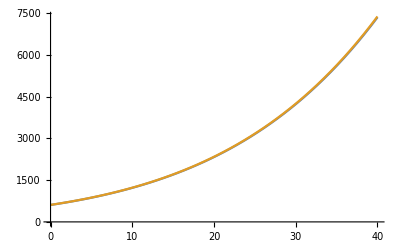

```mathematica
Plot[ {pwater[ t+273.15],100*pwater2[t]}, {t, 0,40}]
```

```mathematica
Md = 0.0289654
```

0.0289654

```mathematica
Mv = 0.018016
```

0.018016

```mathematica
R = 8.314
```

8.314

```mathematica
RhoHumid[T_, phi_] := ( phi pwater[T] Mv + (101325 - phi pwater[T])Md)/R/T;
```

```mathematica
RhoHumid[200,0.56]
```

1.76505

```mathematica
NumberForm[%,10]
```

1.76504522

```mathematica
NumberForm[1.2124653275971196,10]
```

1.212465328